```mathematica
ClearAll["Global`*"]
```

```mathematica
ps=Range[0.01,50,0.1];
```

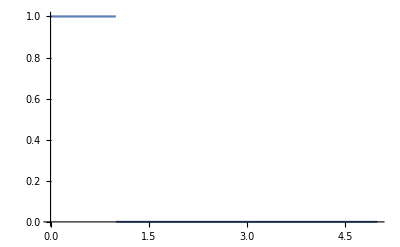

```mathematica
ϕ[r_]=HeavisideTheta[1-r];
Plot[ϕ[r],{r,0,5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {1.00494}. NIntegrate obtained -0.317965 and 0.000806564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {1.00494}. NIntegrate obtained -0.322817 and 0.000817644 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {1.00494}. NIntegrate obtained -0.331199 and 0.000835509 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

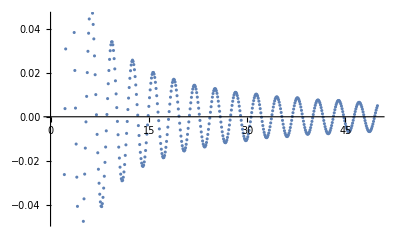

```mathematica
ϕ[r_]=HeavisideTheta[1-r];
ps=Range[0.01,50,0.1];

dr=0.01;
rmin=0.01;
rmax=10;
rs=Range[rmin,rmax,dr];

fNintps=NIntegrate[r*ps*ϕ[r]*BesselJ[0,r*ps]*BesselY[1,ps],{r,rmin,rmax}];
fSum[p_]=dr*Total[rs*p*ϕ[rs]*BesselJ[0,rs*p]*BesselY[1,p]];
fSumps=fSum[ps];

A=ListPlot[{
Transpose@{ps,fNintps},
Transpose@{ps,fSumps}
}]
```

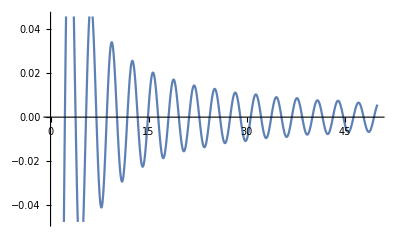

```mathematica
f[p_]=Integrate[r*p*ϕ[r]*BesselJ[0,r*p]*BesselY[1,p],{r,rmin,rmax}];
B=Plot[f[p],{p,0,50}]
```

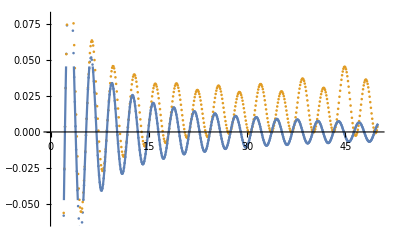

```mathematica
Show[A,B]
```

```mathematica
Install["/media/tobias/data/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/Mathematica/Cuhre-Linux"]
Install["/media/tobias/data/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/Mathematica/Vegas-Linux"]
Install["/media/tobias/data/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/Mathematica/Suave-Linux"]
Install["/media/tobias/data/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/Mathematica/Divonne-Linux"]
```

LinkObject[…]

LinkObject[…]

LinkObject[…]

«1 more identical outputs»

```mathematica
f[x_,y_]=(1+x*y)/(√(2+x^2));
Cuhre[1/(√(1-y^2)√(f[x,y]^2-1)),{x,0.5,10},{y,(√(2+x^2)-1)/x,1},Verbose->0]
```

Cuhre::success: Needed 9035 function evaluations on 70 subregions.

{{15.96,0.0151969,4.4213×10^-18}}

```mathematica
Suave[1/(√(1-y^2)√(f[x,y]^2-1)),{x,0.5,10},{y,(√(2+x^2)-1)/x,1},Verbose->0]
```

Suave::accuracy: Desired accuracy was not reached within 50000 function evaluations on 50 subregions.

{{15.9259,0.0161759,1.}}

```mathematica
Vegas[1/(√(1-y^2)√(f[x,y]^2-1)),{x,0.5,10},{y,(√(2+x^2)-1)/x,1},Verbose->0]
```

Vegas::success: Needed 32500 function evaluations.

{{15.9493,0.0153094,0.0119089}}

```mathematica
ClearAll["Global`*"]
w[p_,m_]=Sqrt[p*p+m*m];
absgradg[t_,u_,v_,p_]=√((-t*u*w[p,mb]/w[t*Q,ma]*Q^2+Q*p*v)^2+(w[t*Q,ma]*w[p,mb])^2+(t*Q*p)^2);
areafactor[t_,v_,p_]=√((v*(p*Q)/(w[p,mb]*w[t*Q,ma])*(1-(t^2*Q^2)/w[t*Q,ma]^2))^2+(1)^2+((t*Q*p)/(w[t*Q,ma]*w[p,mb]))^2);
ustar[t_,v_,p_]=(ma*Eabc+Q*p*t*v)/(w[t*Q,ma]*w[p,mb]);
Integrand[t_,v_,p_]=If[ustar[t,v,p]>1,t*1/(√(ustar[t,v,p]^2-1))*1/(√(1-v^2))*areafactor[t,v,p]/absgradg[t,ustar[t,v,p],v,p],0];
IntegrandExplicit[t_,v_,p_]=t*1/(√(ustar[t,v,p]^2-1))*1/(√(1-v^2))*(√((v*(p*Q)/(w[p,mb]*w[t*Q,ma])*(1-(t^2*Q^2)/w[t*Q,ma]^2))^2+(1)^2+((t*Q*p)/(w[t*Q,ma]*w[p,mb]))^2))/(√((-t*√(ustar[t,v,p]^2-1)*w[p,mb]/w[t*Q,ma]*Q^2+Q*p*v)^2+(w[t*Q,ma]*w[p,mb])^2+(t*Q*p)^2))//Simplify
```

(t √(1+(p^2 Q^2 (2 ma^2 Q^2 t^4+Q^4 t^6+ma^4 (t^2+v^2)))/((mb^2+p^2) (ma^2+Q^2 t^2)^3)))/(√(1-v^2) √(-1+(Eabc ma+p Q t v)^2/((mb^2+p^2) (ma^2+Q^2 t^2))) √(p^2 Q^2 t^2+(mb^2+p^2) (ma^2+Q^2 t^2)+(p Q v-(√(mb^2+p^2) Q^2 t √(-1+(Eabc ma+p Q t v)^2/((mb^2+p^2) (ma^2+Q^2 t^2))))/(√(ma^2+Q^2 t^2)))^2))

```mathematica
s=Solve[1==ustar[t,v,p],v];
v1[t_,p_]=v/.s[[1]]//Simplify;
t1min[p_]=t/.Solve[0==D[v1[t,p],t],t][[2]]//FullSimplify;
vmin[p_]=v1[t1min[p],p]//FullSimplify;
s2=Solve[1==v1[t,p],t]//FullSimplify;
tmin[p_]=t/.s2[[1]]//FullSimplify;
tmax[p_]=t/.s2[[2]]//FullSimplify;
Print["v(t,p)|u==1:",v1[t,p], "(=:v1(t,p))"]
Print["v1=min(v1(t,p) at t=",t1min[p]]
Print["min(v1(t,p))=",vmin[p]]
Print["tmin(p)=",tmin[p]]
Print["tmax(p)=",tmax[p]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

v(t,p)|u==1:(-Eabc ma+√(mb^2+p^2) √(ma^2+Q^2 t^2))/(p Q t)(=:v1(t,p))

v1=min(v1(t,p) at t=(√(ma^2 (-Eabc^2+mb^2+p^2)))/(Eabc Q)

min(v1(t,p))=(Eabc (-Eabc ma+√(mb^2+p^2) √((ma^2 (mb^2+p^2))/Eabc^2)))/(p √(ma^2 (-Eabc^2+mb^2+p^2)))

tmin(p)=(Eabc ma p-√((ma^2 (Eabc-mb) (Eabc+mb) (mb^2+p^2))/Q^2) Q)/(mb^2 Q)

tmax(p)=(Eabc ma p+√((ma^2 (Eabc-mb) (Eabc+mb) (mb^2+p^2))/Q^2) Q)/(mb^2 Q)

```mathematica
Q=1;
ma=0.6;
mb=0.14;
mc=0.14;
pabc=Sqrt[((ma+mb)^2-mc^2)*((ma-mb)^2-mc^2)]/(2*ma);
Eabc=Sqrt[mb^2+pabc^2];
```

```mathematica
Manipulate[
Plot[
v1[t,p],{t,0.01,10},
PlotRange->{
{0,10},
{-1,1}
},
Epilog->{(*add lines*)
InfiniteLine[{0,vmin[p]},{1,0}],
InfiniteLine[{tmin[p],0},{0,1}],
InfiniteLine[{tmax[p],0},{0,1}]}
],
{p,0.001,2}]
```

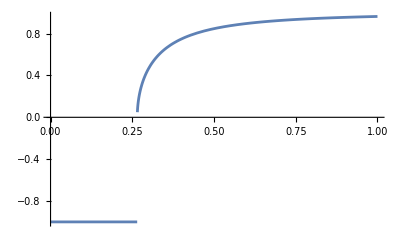

Greater::nord: Invalid comparison with 2.1428+0.0000369841 ⅈ attempted.

Greater::nord: Invalid comparison with 2.14131+0.036956 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with 4.5916-0.0135359 ⅈ attempted.

Greater::nord: Invalid comparison with 4.5916-0.0129834 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

```mathematica
LowerBoundV[p_]=If[Element[vmin[p],Reals],vmin[p],-1];
Plot[LowerBoundV[p],{p,0,1}]
Manipulate[
Plot3D[Integrand[t,v,p],
{t,Max@{0,tmin[p]},tmax[p]},
{v,LowerBoundV[p],1},
PlotRange->{Automatic,Automatic,Automatic}],
{p,0.001,2}]
Manipulate[
Plot[Integrand[t,vmin[p]+(1.0-vmin[p])*0.5,p]/p,
{t,Max@{0,tmin[p]},tmax[p]}],
{p,0.001,2}]
Manipulate[
Plot[Integrand[t1min[p],v,p]/p,
{v,LowerBoundV[p],1}],
{p,0.001,2}]
```

```mathematica
Install[StringJoin[NotebookDirectory[],"Cuhre-Linux"]];
Install[StringJoin[NotebookDirectory[],"Vegas-Linux"]];
```

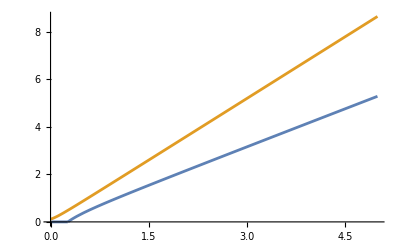

```mathematica
Plot[{Max@{0,tmin[p]},0.1*tmax[p]},{p,0,5}]
```

```mathematica
MyIntegral[p_]:=Cuhre[Evaluate[Integrand[t,v,p]],
{t,Max@{0,tmin[p]},tmax[p]},
{v,LowerBoundV[p],1},
Verbose->0,MaxPoints->1000000][[1]];
```

```mathematica
ps=Array[#&,10,{1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
MyIntegrals=Map[MyIntegral,ps]
(*
MyIntegral[p_]:=Cuhre[Evaluate[Integrand[t,v,p]],
{t,Max@{0,tmin[p]},tmax[p]},
{v,LowerBoundV[p],1},
Verbose->0,MaxPoints->1000000][[1]];

ps=Array[#&,10,{1,10}];

MyIntegrals=Map[MyIntegral,ps]=
{{25.414042761474075,1.2836660435954368,0.},{25.41080892854345,1.245647241303033,0.},{25.41033158296047,1.256972339006273,0.},{25.414420017512317,1.272390716613392,0.},{25.41292776996544,1.2770637500661666,0.},{25.412931416918735,1.2800385231905287,0.},{25.409315122218313,1.267577697812272,0.},{25.413780029751674,1.28015482703711,0.},{25.412992747450406,1.2712650129390797,0.},{25.410965645018326,1.261769745493608,0.}};
*)
```

Cuhre::accuracy: Desired accuracy was not reached within 1000025 function evaluations on 7693 subregions.

General::stop: Further output of Cuhre::accuracy will be suppressed during this calculation.

{{25.414,1.28367,0.},{25.4108,1.24565,0.},{25.4103,1.25697,0.},{25.4144,1.27239,0.},{25.4129,1.27706,0.},{25.4129,1.28004,0.},{25.4093,1.26758,0.},{25.4138,1.28015,0.},{25.413,1.27127,0.},{25.411,1.26177,0.}}